# Final Amplitud

## Max coefficient value in the final time

We need to import the files “cT3.txt”,”cT5.txt” and “cT7.txt”.  This files where generated in the “fourier coefficient for Figure 4” notebook. This files can be find the  same folder.

## Data importation

### Data Import: (*change it to the local directory where the “cT3.txt”,”cT5.txt” and ”cT7.txt” files are*)

```mathematica
directorio="(*your directory here*)\\"
```

C:\Users\DELL\Documents\Aldo\Figura 4\

### Data importation

We need to remember that :

 b=1.76921 for  n3
 b=1.82272 for n5 and 
 b=1.903 for n7

```mathematica
n3(*n,time, fourier coefficient*)=Import[StringJoin[directorio,"cT3.txt"],"TSV"];
n5(*n,time, fourier coefficient*)=Import[StringJoin[directorio,"cT5.txt"],"TSV"];
n7(*n,time, fourier coefficient*)=Import[StringJoin[directorio,"cT7.txt"],"TSV"];
n3=ToExpression[n3];
n5=ToExpression[n5];
n7=ToExpression[n7];
```

## Tables of values

Now with the imported data we look for the maximum value for each row of our matrix, that is, for the different n.b4s

```mathematica
(*max value tables*)
mx3=Table[Position[n3⟦n,t⟧,Max[Abs[ToExpression[n3⟦n,t⟧⟦2;;⟧]]]]⟦1,1⟧,{n,1,Dimensions[n3]⟦1⟧},{t,1,Dimensions[n3]⟦2⟧}];
mx5=Table[Position[n5⟦n,t⟧,Max[Abs[ToExpression[n5⟦n,t⟧⟦2;;⟧]]]]⟦1,1⟧,{n,1,Dimensions[n5]⟦1⟧},{t,1,Dimensions[n5]⟦2⟧}];
mx7=Table[Position[n7⟦n,t⟧,Max[Abs[ToExpression[n7⟦n,t⟧⟦2;;⟧]]]]⟦1,1⟧,{n,1,Dimensions[n7]⟦1⟧},{t,1,Dimensions[n7]⟦2⟧}];
```

We take the last time

```mathematica
cmn3=Transpose[mx3]⟦3⟧;
cmn5=Transpose[mx5]⟦3⟧;
cmn7=Transpose[mx7]⟦3⟧;
```

```mathematica
(*max value index*)
gra3=Table[n3⟦i,-1,cmn3⟦i⟧⟧,{i,1,Length[cmn3]}];
gra5=Table[n5⟦i,-1,cmn5⟦i⟧⟧,{i,1,Length[cmn5]}];
gra7=Table[n7⟦i,-1,cmn7⟦i⟧⟧,{i,1,Length[cmn7]}];
```

```mathematica
(*data for the plot*)
c3=Transpose[{cmn3-1,Flatten[gra3]}]
c5=Transpose[{cmn5-1,Flatten[gra5]}]
c7=Transpose[{cmn7-1,Flatten[gra7]}]
```

{{14,0.263674},{14,0.263814},{15,0.257363},{16,0.220249},{15,0.25727}}

{{15,0.388513},{12,0.363554},{13,0.406069},{14,0.408494},{15,0.389034},{16,0.353896},{17,0.305716},{15,0.38864},{15,0.388664}}

{{15,0.499934},{11,0.479047},{12,0.53704},{13,0.547826},{14,0.538054},{15,0.513904},{16,0.479724},{17,0.438867},{13,0.537278},{13,0.541968},{13,0.543262}}

Since there are some index that are inestable we change the final max fourier coefficient index to the initial max fourier coefficient:

```mathematica
c3⟦1,1⟧=13;
c3⟦5,1⟧=17;

c5⟦1,1⟧=11;
c5⟦2,1⟧=12;
c5⟦8,1⟧=18;
c5⟦9,1⟧=19;

c7⟦1,1⟧=10;
c7⟦2,1⟧=11;
c7⟦9,1⟧=18;
c7⟦10,1⟧=19;
c7⟦11,1⟧=20;
```

We define a list with just the stable points, the ones that stay in the inicial max fourier coefficient.

```mathematica
c3i=c3⟦2;;Length[c3]-1⟧;
c5i=c5⟦2;;Length[c5]-2⟧;
c7i=c7⟦3;;Length[c7]-3⟧;
```

## Plots

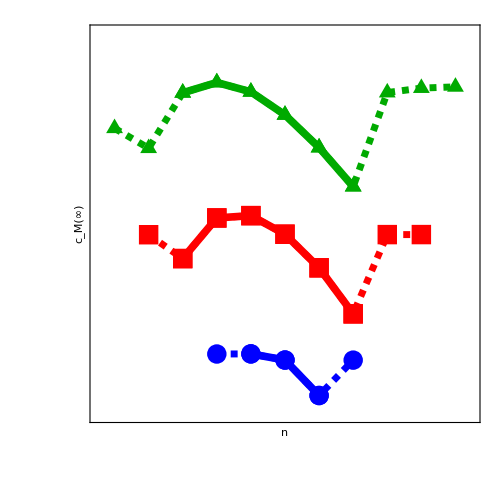

```mathematica
finalyCs=ListPlot[Join[{c3,c5,c7},{c3i,c5i,c7i}],Joined->True,PlotRange->{{9.5,20.5},{.2,.6}},AspectRatio->1,PlotStyle->{{Dashed,Blue,Thickness[0.01]},{Dashed,Red,Thickness[0.01]},{Dashed,Darker[Green],Thickness[0.01]},{Blue,Thickness[0.011]},{Red,Thickness[0.011]},{Darker[Green],Thickness[0.011]}},PlotMarkers->{{"●",20},{"■",20},{"▲",20},{"●",20},{"■",20},{"▲",20}},Frame->True, FrameTicks->{{None,{.2,.4,.6}},{None,{11,13,15,17,19}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["n",38,Italic, Black]],Text[Style["c_M(∞)",38,Italic, Black]]},InterpolationOrder->1]
```

```mathematica
Export["figura4partea.png",finalyCs,ImageResolution->250]
```

figura4partea.png